```mathematica
hbar:=6.582119514*(10^(-16)); (*eV.s*)
mu:=5.183*(10^(-29));(*eV.s^2/A^2*)
L :=0.18*((10)^(10));(*em A 18 cm*)
```

```mathematica
(*DISTRIBUIÇÃO DE ENERGIA CINÉTICA*)

R0pp[Ec_]:=-2.8665358678759176*(10^(-5))*(Ec^3)+0.0031928293588166325*(Ec^2)-0.15784348971912937*(Ec)+3.1348994041210845;

dR0dEpp[Ec_]:=-3*2.8665358678759176*(10^(-5))*(Ec^2)+2*0.0031928293588166325*(Ec)-0.15784348971912937;

f0pp[Ec_]:=2.139*Exp[-32.882((R0pp[Ec]-0.74212)^2)];
```

```mathematica
(*Para os dois átomos*)
gn0pp[Ec_]:=((Abs[f0pp[Ec]])^2)*Abs[(dR0dEpp[Ec])];
```

```mathematica
(*Para cada átomo*)
g01pp[Ec_]:=gn0pp[2*Ec];
```

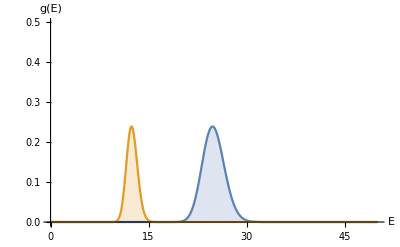

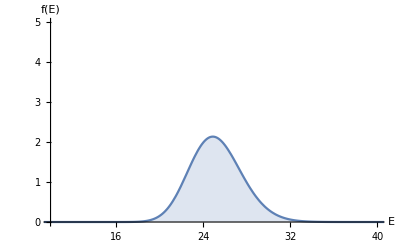

```mathematica
Plot[{gn0pp[Ec],g01pp[Ec]},{Ec,0,50}, Filling->Bottom, AxesLabel->{"E","g(E)" },PlotRange -> {{0, 50}, {0, 0.5}}]

Plot[{f0pp[Ec]}, {Ec,0,50}, Filling->Bottom, AxesLabel->{"E","f(E)" },PlotRange -> {{10, 40}, {0, 5}}]
```

```mathematica
NIntegrate[{gn0pp[Ec]}, {Ec,0,∞}]
```

{1.00001}

```mathematica
f0pp1[R_]:=2.139*Exp[-32.882((R-0.74212)^2)];
```

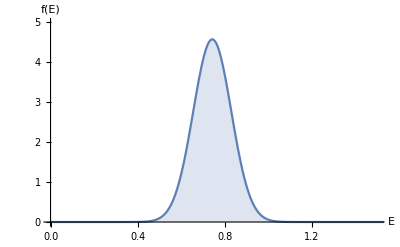

```mathematica
Plot[{(f0pp1[R])^2}, {R,0,2}, Filling->Bottom, AxesLabel->{"E","f(E)" },PlotRange -> {{0, 1.5}, {0, 5}}]
```

```mathematica
NIntegrate[{(f0pp1[R])^2}, {R,0.6306353832413667,0.8872245404202529}]
```

{0.851438}